# 23 Cholesky Decomposition

It is not uncommon for matrices to be symmetric A=Aᵀ  and positive definite i.e.
	x.A.x>0 for x≠0
Amongst other things SPD means that A has only positive real eigenvalues!  It also means you can compute a symmetric LU decomposition 
	A=Rᵀ.R	
with R upper triangular without pivoting.  There is an entirely equivalent version with lower triangular L.

Officially this Cholesky decomposition takes half the flops of an LU decomposition.  Practically the fact that you do not need to pivot means it frequently takes less than half the time.

{0.0005073,C}

{0.0021813,LU}

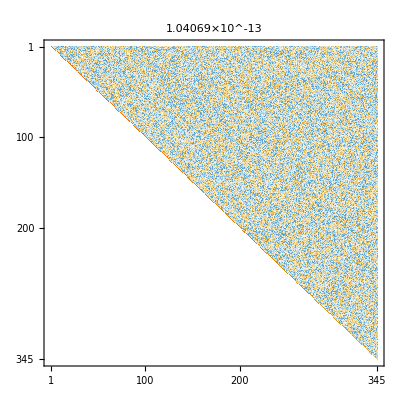

```mathematica
m=345;
A=RandomReal[{-1,1},{m,m}]; A= Aᵀ.A;
AbsoluteTiming[R=CholeskyDecomposition[A];"C"]
AbsoluteTiming[LUDecomposition[A];"LU"]
MatrixPlot[R,PlotLabel->Norm[A-Rᵀ.R]]
```

The question is how to work out and arrange the algorithm.

## Start Small: m=2

Suppose I have a positive symmetric positive definite 2×2 matrix
	(a11 | a12
a12 | a22)
Note a11>0.  Our target is to write this matrix as 
	(a11 | a12
a12 | a22)=(b1 | 0
b2 | b3).(b1 | 0
b2 | b3)^ᵀ=(b1 | 0
b2 | b3).(b1 | b2
0 | b3)=(b1^2 | b1*b2
b1*b2 | b2^2+b3^2)
This works if 
	a11  | = | b1^2 
a12 | = | b1 b2
a22 | = | b2^2+b3^2
Solving this we get 
	b1 | = | √a11
b2 | = | a12/b1
b3 | = | √(a22-b2^2)
Here is a baby function

```mathematica
Chol2[A_]:= Module[{b1,b2,b3},
b1=√A⟦1,1⟧;
b2=A⟦1,2⟧/b1;
b3=√(A⟦2,2⟧-b2^2);
({{b1, b2}, {0, b3}})
]
```

As always test!

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A =A.Aᵀ;
R=Chol2[A];
Norm[A-Rᵀ.R]
```

2.22045×10^-16

## Try Bigger: m=3

Suppose I have a positive symmetric positive definite 2×2 matrix
	(a11 | a12 | a13
a12 | a22 | a23
a13 | a23 | a33)
Note a11>0.  Our target is to write this matrix as 
	(a11 | a12 | a13
a12 | a22 | a23
a13 | a23 | a33)=(b1 | 0 | 0
b2 | b3 | 0
b4 | b5 | b6).(b1 | 0 | 0
b2 | b3 | 0
b4 | b5 | b6)^ᵀ=(b1^2 | b1 b2 | b1 b4
b1 b2 | b2^2+b3^2 | b2 b4+b3 b5
b1 b4 | b2 b4+b3 b5 | b4^2+b5^2+b6^2)
The top row and the left most columns work if 
	a11  | = | b1^2 
a12 | = | b1 b2
a13 | = | b1b4
Note we are going to worry about the rest latter. Solving this we get 
	b1 | = | √a11
(b2
b4) | = | (a12
a13)/b1
We can go down a dimension (on the top and the side) which will leave us with a 2×2 that we already worked out how to do. The way to organize this incremental approach is as follows
	(a11 | wᵀ
w | K)=(α | 0
w/α | I).(1 | 0
0 | K̂).(α | wᵀ/α
0 | I)=(α^2 | wᵀ
w | K̂+1/α^2 w.wᵀ)
where if you expand stuff out (along the row and down the column) we need
	α^2 | = | a11
K̂+1/α^2 w.wᵀ | = | K
Solving for the stuff we do not know we get
	α | = | √a11 |   |  
K̂ | = | K-1/α^2 w.wᵀ | = | K-1/a11 w⊗w
Note this recipe works for a general m.

## General m: Algorithm 23.1

```mathematica
Clear[CholeskyBook]
CholeskyBook[A_]:= Module[{R=A,m=Length[A]},
Do[
Do[
R⟦j,j;;m⟧=R⟦j,j;;m⟧-R⟦k,j;;m⟧ R⟦k,j⟧/R⟦k,k⟧,
{j,k+1,m}];
R⟦k,k;;m⟧=R⟦k,k;;m⟧/√R⟦k,k⟧,
{k,1,m}];
UpperTriangularize[R]]
```

As always test!

```mathematica
m=523;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+ IdentityMatrix[m];
AbsoluteTiming[R=CholeskyBook[A];]
MatrixPlot[R,PlotLabel->Norm[A-Rᵀ.R]]
```

{2.60476,Null}

-Graphics-

## General m: Other Organizational Schemes Outer Product

There are lots of ways to organize this.

```mathematica
Clear[CholeskyOuterProduct]
CholeskyOuterProduct[A_]:= Module[{R=A,m=Length[A],col},
Do[
col=R⟦k,k+1;;m⟧;
R⟦k+1;;m,k+1;;m⟧=R⟦k+1;;m,k+1;;m⟧-KroneckerProduct[col,col]/R⟦k,k⟧;
R⟦k,k;;m⟧=R⟦k,k;;m⟧/√R⟦k,k⟧,
{k,1,m}];
UpperTriangularize[R]]
```

As always test!

```mathematica
m=523;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+ IdentityMatrix[m];
AbsoluteTiming[R=CholeskyOuterProduct[A];]
MatrixPlot[R,PlotLabel->Norm[A-Rᵀ.R]]
```

{0.537605,Null}

-Graphics-

## General m: Other Organizational Schemes Outer Product and “In Place”

There are lots of ways to organize this.

```mathematica
Clear[CholeskyInPlaceOP]
SetAttributes[CholeskyInPlaceOP,HoldFirst]
CholeskyInPlaceOP[R_]:= Module[{m=Length[R],col},
Do[
col=R⟦k,k+1;;m⟧;
R⟦k+1;;m,k+1;;m⟧=R⟦k+1;;m,k+1;;m⟧-KroneckerProduct[col,col]/R⟦k,k⟧;
R⟦k,k;;m⟧=R⟦k,k;;m⟧/√R⟦k,k⟧,
{k,1,m}];
R=UpperTriangularize[R];]
```

As always test!

```mathematica
m=523;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+ IdentityMatrix[m];
R=A;
AbsoluteTiming[CholeskyInPlaceOP[R]]
MatrixPlot[R,PlotLabel->Norm[A-Rᵀ.R]]
```

{0.56006,Null}

-Graphics-

## Cholesky Race

The obvious question is which is better.  The obvious answer is the built in highly optimized code!

```mathematica
m=523;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+ IdentityMatrix[m];
AbsoluteTiming[CholeskyDecomposition[A];]
AbsoluteTiming[CholeskyBook[A];]
AbsoluteTiming[CholeskyOuterProduct[A];]
AbsoluteTiming[R=A;CholeskyInPlaceOP[R];]
```

{0.0012734,Null}

{0.796432,Null}

{0.550135,Null}

{0.648328,Null}

```mathematica
m=523;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+ IdentityMatrix[m];
Timing[CholeskyDecomposition[A];]
Timing[CholeskyBook[A];]
Timing[CholeskyOuterProduct[A];]
Timing[R=A;CholeskyInPlaceOP[R];]
```

{0.,Null}

{0.765625,Null}

{0.203125,Null}

{0.28125,Null}

in any computational system there are different ways to time things.  In Mathematica:
	Timing gives the CPU time used.
	AbsoluteTiming gives the elapsed time.

## Solving A.x=b with a Cholesky when A is SPD.

Cholesky is more stable, guaranteed stable, and usually a smidge faster.

```mathematica
m=3345;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
{x1,x2}=RandomReal[{-1,1},{2,m}];
{b1,b2}={A.x1,A.x2};
{"LU",AbsoluteTiming[LUSolver=LinearSolve[A];],AbsoluteTiming[{x1LU,x2LU}=Map[LUSolver,{b1,b2}];]}
{"Chol",AbsoluteTiming[CholSolver=LinearSolve[A,Method->"Cholesky"];],AbsoluteTiming[{x1Chol,x2Chol}=Map[CholSolver,{b1,b2}];]}
TableForm[Map[Norm,{{x1-x1LU,x1-x1Chol},{x2-x2LU,x2-x2Chol}},{2}],
TableHeadings->{{"x1","x2"},{"LU","Chol"}}]
```

{LU,{0.24316,Null},{0.0154813,Null}}

{Chol,{0.202669,Null},{0.01102,Null}}

| LU | Chol
x1 | 1.35404×10^-8 | 1.14154×10^-8
x2 | 3.01402×10^-9 | 2.91186×10^-9

If you want to do this by hand you compute triangular factors to get Rᵀ.R.x=b.  Insert parenthesis to get
	Rᵀ.(R.x)=b
and define y=R.x to get the sequence of triangular solves 
	Rᵀ.y=b⟶ỹ
and 
	R.x=ỹ⟶x̃.  The small time saving for the Cholesky back-solve is due to the coefficient matrices being related!